```mathematica
allelefreq[tot_]:=Block[{w,dd,r1,r2,tottot},
w=Table[tot[[i,2]]+.5tot[[i,3]]+.5tot[[i,4]]+.5tot[[i,5]],{i,Length[tot]}];

dd=Table[tot[[i,6]]+.5tot[[i,3]]+.5tot[[i,7]]+.5tot[[i,8]],{i,Length[tot]}];
r1=Table[tot[[i,9]]+.5tot[[i,4]]+.5tot[[i,7]]+.5tot[[i,10]],{i,Length[tot]}];
r2=Table[tot[[i,11]]+.5tot[[i,5]]+.5tot[[i,8]]+.5tot[[i,10]],{i,Length[tot]}];

tottot=(0.1+Total[Transpose[tot[[All,2;;11]]]]);
N[{w/tottot,dd/tottot,r1/tottot,r2/tottot}]];
```

```mathematica
(*------ Change to won directory-----*)
SetDirectory["~/Dropbox/Doublesex/Resistance/Evolution/InLocResis"];
```

```mathematica
xibli
```

{0.,0.2,0.4,0.6}

```mathematica
xili=Range[0,0.8,0.2];
mutcostli=Range[0,0.5,0.1];
```

{0.,0.1,0.2,0.3,0.4,0.5}

```mathematica
Do[pa=Flatten[{numruns=1,maxT=15000,NumPat=50,muJ=0.05,muA=0.125,beta=100,theta=9,meanTL=0.0667,mindev=10,gamma=(1-0.95)/2,xiA=xili[[xx]],xiB=0,eA=0.95,eB=0.95,drivertime=100,NumDriver=1000,NumDriverPat=1,d=0.00001,Ld=0.2,psi=0,muAES=0.9,thide1=300,thide2=350,twake1=140,twake2=170,al0=200000,al0var=0.,al1=0,amp=0,resp=1,recstart=10,recend=10000,recIntGlob=10,recIntLoc=500,recsitesfreq=1,set=10 mm+xx,"t","r",nummut=0,muttime=1000,mutgen=2,mutcost=mutcostli[[mm]],mutsites=10}];
Export["Par"<>ToString[set]<>".csv",pa,"CSV","TextDelimiters"->""],{xx,Length[xili]},{mm,Length[mutcostli]}];
```

```mathematica
cout=Import["!../build/gdsimsapp<./Par"<>ToString[set]<>".csv","Table"];
```

{401,11}

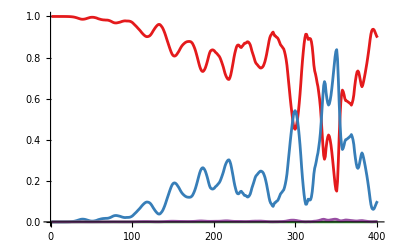

```mathematica
totals=Drop[Import["./output_files/Totals"<>ToString[set]<>"run1.txt","Table"],2];
Dimensions[totals]
(*-----------------------------------------------------------------------*)

(*-------plot the output, both with arithmetic and log y-axis scale----------------------------------------*)
colours={Red,Blue,Green,Orange,Purple,Cyan};
(*ListLinePlot[Table[totals[[All,{1,i}]],{i,2,7,1}],PlotRange->All,PlotStyle->colours,PlotLegends->{"Mww","Mwd","Mdd","Mwr","Mrr","Mdr"}]
ListLogPlot[Table[totals[[All,{1,i}]],{i,2,7,1}],PlotRange->All,PlotStyle->colours,Joined->True,PlotLegends->{"Mww","Mwd","Mdd","Mwr","Mrr","Mdr"}];*)
{ww,dd,r1,r2}=allelefreq[totals];
cc={RGBColor[Rational[76, 85], Rational[26, 255], Rational[28, 255]],RGBColor[Rational[11, 51], Rational[42, 85], Rational[184, 255]],RGBColor[Rational[77, 255], Rational[35, 51], Rational[74, 255]],RGBColor[Rational[152, 255], Rational[26, 85], Rational[163, 255]]};
ListLinePlot[{ww,dd,r1,r2},PlotStyle->cc,PlotRange->All]
```

```mathematica
Table[Total[totals[[All,i]]],{i,2,11,1}]
```

{783904,289041,121855,134430,160670,110932,88446,69763,155320,96443}

```mathematica
ListLinePlot[]
```